```mathematica
Needs["ErrorBarPlots`"]
SetDirectory[NotebookDirectory[]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@Options[g,PlotRange],Sequence@@Options[g,Epilog]]
file=OpenRead["mechanisms/gri30.cti"];
test=ReadList[file,"String"];
Close[file];
slst=StringSplit[Extract[test,Position[test,u_/;StringQ[u]&&First[StringSplit[u,"("]]=="species"]],"\""][[All,2]];
alst=Partition[#,2]&/@StringSplit[StringTrim[StringSplit[Extract[test,Position[test,u_/;StringQ[u]&&First[StringSplit[u,"("]]=="species"]+1],"\""][[All,2]]],{"  ",":"}];
sensitivities=Flatten[Import["data/air/ms.dat"]];
```

/home/zack/cantera/ratemeasure

### Full model ignition peaks

data/air/

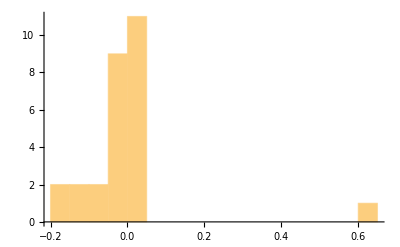

-0.00584123

0.14005

{1.0069,0.988408,0.892233,0.999892,1.00266,0.772576,1.03447,0.869341,0.684155,0.994889,0.979084,0.706133,1.00518,1.00569,0.944681,1.00482,1.00904,0.945569,1.02454,4.38919,0.912221,1.05244,1.00439,0.738068,1.0352,0.966577,0.814966}

```mathematica
filebase="data/air/"
individuals=Table[First@Import[filebase<>"individual/"<>ToString[i]<>"norms.dat"],{i,1,27}];
Histogram[Log[individuals[[All,6]]]/Log[10]]
Mean[Log[individuals[[All,6]]]/Log[10]]
StandardDeviation[Log[individuals[[All,6]]]/Log[10]]
N[individuals[[All,6]],3]
```

```mathematica
itimes={};
imaxes={};
plots={};
ns=53;
filebase="data/air/"
species=Import[filebase<>"species.dat"][[1]];
Monitor[Do[
times=BinaryReadList[filebase<>"times_"<>ToString[n]<>".npy","Real64"][[17;;-1]];
Oind=First@FirstPosition[species,"O"];
concentrations=Transpose[Partition[BinaryReadList[filebase<>"moles_"<>ToString[n]<>".npy","Real64"][[17;;-1]],ns]];
ind=First@FirstPosition[Sign[Differences[concentrations[[Oind]]]],-1];
AppendTo[itimes,times[[ind]]];
AppendTo[imaxes,concentrations[[Oind,ind]]];
AppendTo[plots,
ListPlot[concentrations[[Oind]],PlotStyle->Directive[Black],PlotRange->All,Joined->True,LabelStyle->Directive[16],Axes->False,Frame->True,FrameLabel->{"Time (ms)",DisplayForm[RowBox[{Subscript[X,O],"×",10^HoldForm[5]}]]},ImagePadding->{{75,5},{75,5}},ImageSize->250,AspectRatio->1,FrameStyle->Directive[Black,AbsoluteThickness[1.5]],Epilog->{Red,AbsoluteThickness[2],Line[{{ind,0},{ind,concentrations[[Oind,ind]]}}]}]];,{n,0,26}],n]
2*itimes
imaxes
Manipulate[plots[[i]],{i,1,Length[plots],1}]
```

data/air/

{0.094924,0.126776,0.179856,0.0167348,0.0234416,0.0334884,0.0042168,0.00577216,0.00819672,0.0141568,0.01524,0.018072,0.00190076,0.00233956,0.0030938,0.000519792,0.000662376,0.00089604,0.004008,0.00371332,0.0037924,0.000428796,0.000436304,0.000494508,0.00010412,0.000114356,0.000138432}

{0.0184213,0.0154867,0.000274638,0.0132104,0.0130542,0.000194133,0.00698259,0.00918575,0.0000970263,0.020088,0.0167101,0.000423005,0.0158591,0.0147941,0.000324329,0.00977441,0.0114635,0.000198369,0.0215815,0.0179512,0.000592459,0.0182236,0.0163849,0.000497371,0.0126188,0.0134242,0.000345257}

```mathematica
ScientificForm[itimes/10^-3,2]
ScientificForm[imaxes,2]
```

{4.7×10^1,6.3×10^1,9.×10^1,8.4,1.2×10^1,1.7×10^1,2.1,2.9,4.1,7.1,7.6,9.,9.5×10^-1,1.2,1.5,2.6×10^-1,3.3×10^-1,4.5×10^-1,2.,1.9,1.9,2.1×10^-1,2.2×10^-1,2.5×10^-1,5.2×10^-2,5.7×10^-2,6.9×10^-2}

{1.8×10^-2,1.5×10^-2,2.7×10^-4,1.3×10^-2,1.3×10^-2,1.9×10^-4,7.×10^-3,9.2×10^-3,9.7×10^-5,2.×10^-2,1.7×10^-2,4.2×10^-4,1.6×10^-2,1.5×10^-2,3.2×10^-4,9.8×10^-3,1.1×10^-2,2.×10^-4,2.2×10^-2,1.8×10^-2,5.9×10^-4,1.8×10^-2,1.6×10^-2,5.×10^-4,1.3×10^-2,1.3×10^-2,3.5×10^-4}

{155,158,38,53,156,161,170,32,119,118}

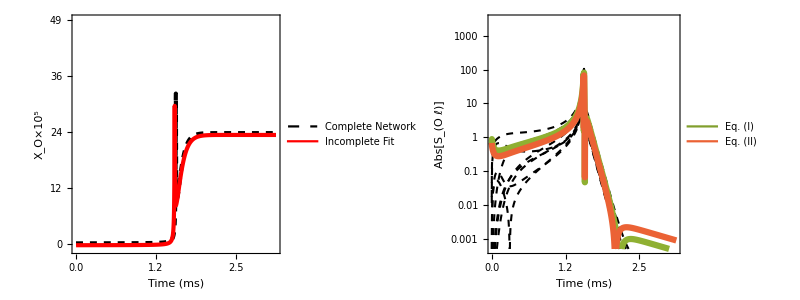

```mathematica
n=14;
filebase="data/air/";
times=BinaryReadList[filebase<>"times_"<>ToString[n]<>".npy","Real64"][[17;;-1]];
species=Import[filebase<>"species.dat"][[1]];
nspecies=Length[species];
concentrations=Transpose[Partition[BinaryReadList[filebase<>"moles_"<>ToString[n]<>".npy","Real64"][[17;;-1]],nspecies]];
sensitivities=Mean[Table[Transpose[Partition[BinaryReadList[filebase<>"obssens_"<>ToString[m]<>".npy","Real64"][[17;;-1]],nreactions]],{m,0,26}]];
fit=Transpose[Partition[BinaryReadList[filebase<>"fit_"<>ToString[n]<>".npy","Real64"][[17;;-1]],nspecies]];
sensitivities=Transpose[Partition[BinaryReadList[filebase<>"obssens_"<>ToString[n]<>".npy","Real64"][[17;;-1]],nreactions]];
Nt=Length[concentrations[[1]]];
cmax=1.5*Max[concentrations[[Oind]],fit[[Oind]]];
topsens=Table[FirstPosition[Table[Norm[sensitivities[[i]],2],{i,1,Length[sensitivities]}],Extract[Sort[Table[Norm[sensitivities[[i]],2],{i,1,Length[sensitivities]}]],-i]][[1]],{i,1,10}]
p4=ListPlot[{concentrations[[Oind]]+0.2*10^-5,fit[[Oind]]-0.2*10^-5},PlotStyle->{Directive[Thickness[0.01],Black,Dashed],Directive[Thickness[0.01],Red]},PlotRange->{All,{-10^-5,cmax}},Joined->True,LabelStyle->Directive[16],Axes->False,Frame->True,FrameLabel->{"Time (ms)",DisplayForm[RowBox[{Subscript[X,O],"×",10^HoldForm[5]}]]}, FrameTicks->{{Table[{i,Round[10.^5*i]},{i,0,cmax,(cmax)/4}],{}},{Table[{i,PaddedForm[tmax*i/(nmax-1),{4,1}]},{i,0,(nmax-1),(nmax-1)/5}],{}}},ImageSize->300,ImagePadding->{{65,20},{55,10}},AspectRatio->1,PlotLegends->Placed[LineLegend[{Directive[Black,Dashed],Red},{Style[Column[{"Complete","Network"}],Background->White],Style[Column[{"Incomplete","Fit"}],Background->White]},LabelStyle->Directive[14],LegendMarkerSize->{{25,10}},LegendLayout->"Row"],{Scaled[{0.01,0.95}],Scaled[{0,1}]}],FrameStyle->Directive[Black,AbsoluteThickness[1.5]]];
eq1=38;
eq2=53;
p5=Legended[ListLogPlot[Join[Abs[Part[sensitivities,Complement[topsens,{eq2,eq1}]]],{Abs[sensitivities[[eq2]]]*1.2,Abs[sensitivities[[eq1]]]*0.8}],PlotStyle->Join[Table[Directive[Thickness[0.005],Dashed,Black],{i,1,Length[topsens]-2}],{Directive[Thickness[0.015],ColorData[97,"ColorList"][[3]]],Directive[Thickness[0.015],ColorData[97,"ColorList"][[4]]]}],PlotRange->{0.5*10^-3,3*10^3},Joined->True,LabelStyle->Directive[16],Axes->False,Frame->True,FrameLabel->{"Time (ms)", Abs[Subscript[S,DisplayForm[RowBox[{O," ",ℓ}]]]]}, FrameTicks->{{Table[With[{n=n},{10^n,HoldForm[10^HoldForm[n]]}],{n,-3,3, 2}],{}},{Table[{i,PaddedForm[tmax*i/(nmax-1),{4,1}]},{i,0,(nmax-1),(nmax-1)/5}],{}}},ImageSize->300,ImagePadding->{{65,20},{55,10}},AspectRatio->1,FrameStyle->Directive[Black,AbsoluteThickness[1.5]]],Placed[LineLegend[{Darker[ColorData[97,"ColorList"][[3]],0.1],ColorData[97,"ColorList"][[4]]},{"Eq. (I)  ","Eq. (II)  "},LabelStyle->Directive[14],LegendMarkerSize->{{25,10}},LegendLayout->"Row"],{Scaled[{0.05,0.95}],Scaled[{0,1}]}]];
Grid[{{p4,p5}}]
```

### Graph plots

5000

3419

{RGBColor[Rational[1, 3], Rational[1, 3], 1],RGBColor[1, Rational[1, 3], Rational[1, 3]]}

{RGBColor[0.165698, 0.282261, 0.936187],RGBColor[0.845274, 0.369528, 0.19115]}

{RGBColor[0.431296, 0.709773, 0.927077],RGBColor[0.898695, 0.686452, 0.6785475]}

{RGBColor[Rational[1, 3], Rational[1, 3], 1],RGBColor[1, Rational[1, 3], Rational[1, 3]]}

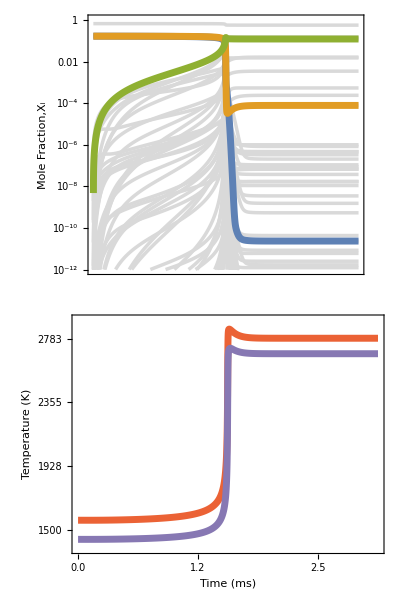

```mathematica
n=14;
filebase="data/air/";
times=BinaryReadList[filebase<>"times_"<>ToString[n]<>".npy","Real64"][[17;;-1]];
species=Import[filebase<>"species.dat"][[1]];
nspecies=Length[species];
concentrations=Transpose[Partition[BinaryReadList[filebase<>"moles_"<>ToString[n]<>".npy","Real64"][[17;;-1]],nspecies]];
Nt=Length[concentrations[[1]]];
rates=BinaryReadList[filebase<>"rates_"<>ToString[n]<>".npy","Real64"][[17;;-1]];
nreactions=Length[rates]/Nt;
rates=Transpose[Partition[rates,nreactions]];
times=BinaryReadList[filebase<>"times_"<>ToString[n]<>".npy","Real64"][[17;;-1]];
temperatures=BinaryReadList[filebase<>"temperatures_"<>ToString[n]<>".npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures_"<>ToString[n]<>".npy","Real64"][[17;;-1]];

Nt=Length[times]
imagePadding2={{75,75},{1,1}};
imgSize2={500,250};
imagePadding1={{75,75},{50,1}};
imgSize1={500,290};
imgSize3={440*(2.2)/(1.3),440};

sptime[text_]:=First@FirstPosition[Accumulate[10^-12+concentrations[[First@FirstPosition[species,text]]]]/Total[10^-12+concentrations[[First@FirstPosition[species,text]]]],u_/;u>0.5]/Nt
sptimemin=Min[sptime/@species];
sptimemax=Max[sptime/@species];
spcol[text_]:=Blend[{Cyan,Orange},(sptime[text]-sptimemin)/(sptimemax-sptimemin)]
vsize[text_]:=0.005+0.08*(Log[Max[Mean[concentrations[[First@FirstPosition[species,text]]]],10^-8]]/Log[10]+8)/8
Oind=First@FirstPosition[species,"O"];

tmax=times[[-1]]/10^-3;
nmax=Length[times];
Tmax=Max[temperatures];
Tmin=Min[temperatures];
Pmax=Max[pressures];
Pmin=Min[pressures];

reactantnames={"CH4","O2","N2"};
productnames={"CO2","H2O","CO"};
ohintermediates={"H2","H","O","OH"};
cmax=1.1*Max[{concentrations[[First@FirstPosition[species,"H2O"]]],concentrations[[First@FirstPosition[species,"CH4"]]][[2]],concentrations[[First@FirstPosition[species,"O2"]]][[2]]}];
cplots={"CH4","O2","H2O"};
ccplots=ColorData[97,"ColorList"][[1;;3]];
p1=ListLogPlot[Join[concentrations,(concentrations[[First@FirstPosition[species,#]]])&/@cplots],Joined->True,PlotRange->{10^-12,1},LabelStyle->Directive[16,Black],Axes->False,Frame->True,FrameLabel->{None,DisplayForm[RowBox[{"Mole Fraction,",Subscript[ X,i]}]]},FrameTicks->{{Automatic,{}},Table[{i,""},{i,0,(nmax-1),(nmax-1)/5}]},PlotStyle->Join[ConstantArray[Directive[Thickness[0.005],LightGray],nspecies],Directive[Thickness[0.01],#]&/@ccplots],Prolog->Join[Inset[Framed[Style[DisplayForm[ToBoxes@Row[Subscript[#[[1]],#[[2]]/."1"->""]&/@SortBy[Extract[alst,FirstPosition[slst,#[[1]]]],First]]],16,#[[2]]],Background->None,FrameStyle->None],{nmax*1.1,Log[concentrations[[First@FirstPosition[species,#[[1]]],-1]]]}]&/@Transpose[{cplots,ccplots}]],ImagePadding->imagePadding2,ImageSize->imgSize2,AspectRatio->Last[imgSize1]/First[imgSize1],FrameStyle->Directive[Black,AbsoluteThickness[1.5]],PlotRangeClipping->False];
p2=ListPlot[{(temperatures-Tmin)/(Tmax-Tmin)+0.05,(pressures-Pmin)/(Pmax-Pmin)-0.05},Joined->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[4]],Thickness[0.01]],Directive[ColorData[97,"ColorList"][[5]],Thickness[0.01]]},PlotRange->{-0.1,1.1},LabelStyle->Directive[16,Black],Axes->False,Frame->True,FrameLabel->{{Style["Temperature (K)",ColorData[97,"ColorList"][[4]]],Style["Pressure (atm)",ColorData[97,"ColorList"][[5]]]},{"Time (ms)",None}},FrameTicks->{{Table[{(T-Tmin)/(Tmax-Tmin),Style[Round[T],ColorData[97,"ColorList"][[4]]]},{T,Tmin,Tmax,(Tmax-Tmin)/3}],Table[{(P-Pmin)/(Pmax-Pmin),Style[PaddedForm[P/101325.,{3,2}],ColorData[97,"ColorList"][[5]]]},{P,Pmin,Pmax,(Pmax-Pmin)/3}]},{Table[{i,PaddedForm[tmax*i/(nmax-1),{4,1}]},{i,0,(nmax-1),(nmax-1)/5}],{}}},ImagePadding->imagePadding1,ImageSize->imgSize1,AspectRatio->Last[imgSize1]/First[imgSize1],FrameStyle->Directive[Black,AbsoluteThickness[1.5]]];
(* Possible bimolecular interactions *)
reacs=Flatten[Table[{i,j},{i,1,Length[alst]},{j,i,Length[alst]}],1];
atoms=DeleteDuplicates[Flatten[alst[[All,All,1]]]];
acount[r_]:=(Total[ToExpression/@Cases[Flatten[alst[[r[[{1,2}]]]],1],u_/;u[[1]]==#][[All,2]]]&/@atoms);
test=acount/@reacs;
test2=Cases[Position[test,#]&/@DeleteDuplicates[test],u_/;Length[u]>1];
stoipairs=slst[[#]]&/@#&/@(Extract[reacs,#]&/@test2);
stoipairs2=Flatten[Subsets[#,{2,2}]&/@stoipairs,1];
Total[Binomial[#,2]&/@(Length/@stoipairs)]
colors={Lighter[Blue],Lighter[Red]}
colors={ColorData["LightTemperatureMap"][0],ColorData["LightTemperatureMap"][1]}
colors={ColorData["Pastel"][1],ColorData["Pastel"][1/4]}
colors={Lighter[Blue],Lighter[Red]}
rlst=Import[filebase<>"norms.dat"];
sensitivities=Flatten[Import[filebase<>"ms.dat"]];
isensitivities=Flatten[Import[filebase<>"mi.dat"]];
Grid[{{p1},{p2}}]
```

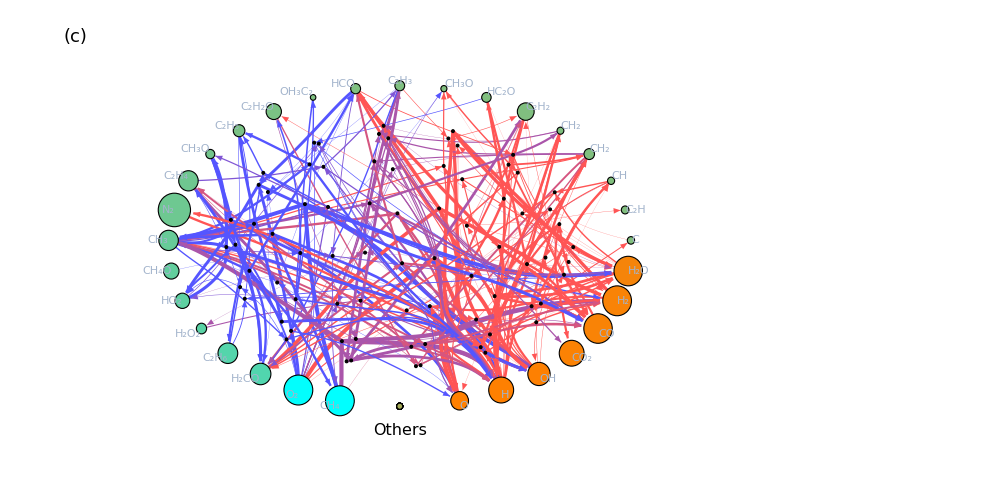
-Graphics- | -Graphics-

```mathematica
r1=1.5;
r2=1;
weights=Mean/@rates;
weights2=First@FirstPosition[Abs[#],Max[Abs[#]]]&/@rates/Nt;
reactants=Import[filebase<>"reactants.dat"][[All,1;;-1;;2]];
products=Import[filebase<>"products.dat"][[All,1;;-1;;2]];
wscale=Max[Abs[weights]];
ethrs=Mean[Abs[weights]]/2;
ethick=0.003;
shown=Flatten[Position[weights,u_/;Abs[u]>ethrs]];
edges=Table[If[weights[[i]]>0,Join[Table[reactants[[i,j]]->i,{j,1,Length[reactants[[i]]]}],Table[i->products[[i,j]],{j,1,Length[products[[i]]]}]],Join[Table[i->reactants[[i,j]],{j,1,Length[reactants[[i]]]}],Table[products[[i,j]]->i,{j,1,Length[products[[i]]]}]]],{i,1,nreactions}];
center=DeleteDuplicates[Join[Flatten[edges[[shown,All,1]]],Flatten[edges[[shown,All,2]]]]];
centerspecies=SortBy[Complement[DeleteDuplicates[DeleteDuplicates[Join[Flatten[edges[[shown,All,1]]],Flatten[edges[[shown,All,2]]]]]],Range[nreactions]],spcol[#]&];
centerreactions=Complement[center,centerspecies];
bottomspecies=SortBy[Complement[species,centerspecies],spcol[#]&];
bottomreactions=Complement[Range[nreactions],centerreactions];
rvcs=GraphEmbedding[PathGraph[Flatten[Position[weights,u_/;Abs[u]>ethrs]],GraphLayout->"SpiralEmbedding"]];
rvcs2=GraphEmbedding[PathGraph[Flatten[Position[weights,u_/;Abs[u]<=ethrs]],GraphLayout->"SpiralEmbedding"]];
{xmax,xmin,ymax,ymin}={Max[rvcs[[All,1]]],Min[rvcs[[All,1]]],Max[rvcs[[All,2]]],Min[rvcs[[All,2]]]};
{xmax2,xmin2,ymax2,ymin2}={Max[rvcs2[[All,1]]],Min[rvcs2[[All,1]]],Max[rvcs2[[All,2]]],Min[rvcs2[[All,2]]]};
transform[p_]:=1.5*{r1,r2}*{(p[[2]]-ymin)/(ymax-ymin)-1/2,(p[[1]]-xmin)/(xmax-xmin)-1/2};
transform2[p_]:=1.5*{r1,r2}*{(p[[2]]-ymin2)/(ymax2-ymin2)-1/2,(p[[1]]-xmin2)/(xmax2-xmin2)-1/2};
trange=Quantile[Extract[weights2,Position[weights,u_/;Abs[u]>ethrs]],{0.25,0.75}];
eweight[edge_]:=If[MemberQ[Range[nreactions],edge[[1]]],weights[[edge[[1]]]],weights[[edge[[2]]]]];
ecolor[edge_]:=If[MemberQ[Range[nreactions],edge[[1]]],weights2[[edge[[1]]]],weights2[[edge[[2]]]]];
vsize[text_]:=0.005+0.08*(Log[Max[Mean[concentrations[[First@FirstPosition[species,text]]]],10^-8]]/Log[10]+8)/8;
sizes={1.0,0.1,0.01,0.001,0.0001};
wsizes=Table[z/.First@Solve[(Log[Abs[z/wscale]]-Log[Abs[ethrs/wscale]])/(0-Log[Abs[ethrs/wscale]])==i*1.0/5,z],{i,5,1,-1}];
vcs=Join[Table[centerspecies[[i]]->{r1*Cos[3*Pi/2-Pi/12-(2*Pi-2*Pi/12)*(i-1)/(Length[centerspecies]-1)],r2*Sin[3*Pi/2-Pi/12-(2*Pi-2*Pi/12)*(i-1)/(Length[centerspecies]-1)]},{i,1,Length[centerspecies]}],
Table[bottomspecies[[i]]->{0,-r2},{i,1,Length[bottomspecies]}],Table[i->If[MemberQ[centerreactions,i],transform[rvcs[[First@FirstPosition[SortBy[Flatten[Position[weights,u_/;Abs[u]>ethrs]],weights2[[#]]&],i]]]],transform2[rvcs2[[First@FirstPosition[SortBy[Flatten[Position[weights,u_/;Abs[u]<=ethrs]],weights2[[#]]&],i]]]]],{i,nreactions}]];
p0=Graph[Join[species,shown],Flatten[edges],GraphLayout->{"EdgeLayout"->"DividedEdgeBundling"},VertexCoordinates->vcs,VertexLabels->(#->If[ValueQ[Element[#,Integers]],None,If[MemberQ[centerspecies,#],If[0.0015*ImageDimensions[Rasterize[Framed[Style[DisplayForm[ToBoxes@Row[If[#[[2]]≠"1",Subscript[#[[1]],#[[2]]],#[[1]]]&/@Sort[Extract[alst,FirstPosition[slst,#]]]]],16,Black],Background->LightGray,FrameStyle->None,RoundingRadius->5,ContentPadding->False]]][[1]]<vsize[#]&&False,Placed[Framed[Style[DisplayForm[ToBoxes@Row[If[#[[2]]≠"1",Subscript[#[[1]],#[[2]]],#[[1]]]&/@Extract[alst,FirstPosition[slst,#]]]],16,Black],Background->None,FrameStyle->None,RoundingRadius->5,Alignment->Center],Center],Placed[Framed[Style[DisplayForm[ToBoxes@Row[If[#[[2]]≠"1",Subscript[#[[1]],#[[2]]],#[[1]]]&/@Extract[alst,FirstPosition[slst,#]]]],16,Black],Background->None,FrameStyle->None,RoundingRadius->5,Alignment->Center,ContentPadding->False],{{1/2,1/2},{1/2,1/2}-(#/Norm[#]/.vcs)}]],None]]&/@Join[species,Range[nreactions]]),VertexStyle->(#->If[ValueQ[Element[#,Integers]],{If[MemberQ[bottomreactions,#],{Opacity[0],EdgeForm[None]},{Opacity[1],EdgeForm[Black]}],Black},If[MemberQ[centerspecies,#],{spcol[#],EdgeForm[Black]},{Opacity[1.0],Blend[spcol/@bottomspecies],EdgeForm[Black]}]]&/@Join[species,Range[nreactions]]),
VertexSize->(#->If[ValueQ[Element[#,Integers]],{"Scaled",0.005},If[MemberQ[centerspecies,#],{"Scaled",0.7*vsize[#]},{"Scaled",0.7*Mean[vsize/@bottomspecies]}]]&/@Join[species,Range[nreactions]]),EdgeStyle->(#-> If[Abs[eweight[#]]<=ethrs,{Directive[Opacity[0]]},{Directive[Opacity[1.0]],Directive[Blend[colors,(ecolor[#]-trange[[1]])/(trange[[2]]-trange[[1]])]],Thickness[Abs[ethick*(Log[Abs[eweight[#]/wscale]]-Log[Abs[ethrs/wscale]])/(0-Log[Abs[ethrs/wscale]])]],Arrowheads[{{Abs[10*ethick*(Log[Abs[eweight[#]/wscale]]-Log[Abs[ethrs/wscale]])/(0-Log[Abs[ethrs/wscale]])],1.0}}]}]&/@Flatten[edges]),EdgeShapeFunction->(If[Position[vcs,First[#]]≠{},{Arrow[#,{0.0,1.5*vsize[vcs[[FirstPosition[N[vcs],Last[#]][[1]],1]]]}]},{Arrow[#,{0.0,0.01}]}]&),ImageSize->{1000,500}];
p=Show[p0,Prolog->{Inset[Grid[{{Graphics[Text[Style["Nodes",16],{0,0}],ImageSize->{125,50}],Graphics[Text[Style["Links",16],{0,0}],ImageSize->{125,50}]},{MatrixPlot[Table[Blend[{Cyan,Orange},(y-sptimemin)/(sptimemax-sptimemin)],{y,sptimemin,sptimemax,(sptimemax-sptimemin)/100},{x,1,100}],AspectRatio->10,ImageSize->{125,175},ImagePadding->{{90,15},{10,5}},FrameTicks->{{Table[{i,PaddedForm[(sptimemin+(i-1)*(sptimemax-sptimemin)/100)*times[[-1]]/10^-3,{3,2}]},{i,1,101,20}],None},{None,None}},PlotRangePadding->None,LabelStyle->Directive[16,Black],FrameLabel->{{None,None},{"Species Time (ms)",None}},RotateLabel->True,DataReversed->{True,True}],MatrixPlot[Table[Directive[Opacity[1.0],Blend[colors,(y-trange[[1]])/(trange[[2]]-trange[[1]])]],{y,trange[[1]],trange[[2]],(trange[[2]]-trange[[1]])/100},{x,1,100}],AspectRatio->10,ImageSize->{125,175},ImagePadding->{{5,90},{10,5}},FrameTicks->{{None,Table[{i,PaddedForm[(trange[[1]]+(i-1)*(trange[[2]]-trange[[1]])/100)*times[[-1]]/10^-3,{5,4}]},{i,1,101,20}]},{None,None}},PlotRangePadding->None,LabelStyle->Directive[16,Black],FrameLabel->{{None,None},{None,"Reaction Time (ms)"}},RotateLabel->True,DataReversed->{True,True}]},{Graphics[{{Table[{EdgeForm[Black],White,Disk[{-1.0,-1.25*i},12*(0.005+0.08*(Log[sizes[[i]]]/Log[10]+8)/8)],Black,Text[Style[With[{n=i},HoldForm[10^(-n)]],16],{-2.8,-1.25*i}]},{i,1,Length[sizes]}]},Rotate[Text[Style["Mole Fraction",16],{-4.0,-4}],Pi/2]},PlotRange->{{-5,0.1},{-8,0}},ImageSize->{125,175}],Graphics[{{Table[{Thickness[10*Abs[ethick*(Log[Abs[wsizes[[i]]/wscale]]-Log[Abs[ethrs/wscale]])/(0-Log[Abs[ethrs/wscale]])]],Line[{{1,-1.25*i},{2,-1.25*i}}],Text[Style[PaddedForm[wsizes[[i]],{2,2}],16],{3,-1.25*i}]},{i,1,Length[sizes]}]},Rotate[Text[Style[DisplayForm[RowBox[{"Rate ","(","mol ",Superscript["m",-3],Superscript["ms",-1],")"}]],16],{4.9,-4}],Pi/2]},PlotRange->{{0.5,6},{-8,0}},ImageSize->{125,175}]}}],{2.6,0.0}],Text[Style["Others",16],{0,-r2-0.15}]},ImageSize->{1000,500},PlotRange->{{-2,3.3},{-1.3,1.25}},PlotRangePadding->None];
p3=Grid[{{Grid[{{Show[p1,Epilog->{Inset[Style["(a)",18],ImageScaled[{0,1}],Scaled[{0,1}]]},PlotRangeClipping->False]},{Show[p2,Epilog->{Inset[Style["(b)",18],ImageScaled[{0,1}],Scaled[{0,1}]]},PlotRangeClipping->False]}},Alignment->Left,Spacings->0],Show[p,Epilog->{Inset[Style["(c)",18],Scaled[{0,1}],Scaled[{0,1}]]}]}},Spacings->0]
Export["fig1.pdf",p3,LineBreakWithin->False];
```

```mathematica
n0=2400;
n1=2600;
Monitor[Do[
weights3=rates[[All,n]]/10;
vsize[text_]:=0.005+0.08*(Log[Max[concentrations[[First@FirstPosition[species,text],n]],10^-8]]/Log[10]+8)/8;
eweight[edge_]:=If[MemberQ[Range[nreactions],edge[[1]]],weights3[[edge[[1]]]],weights3[[edge[[2]]]]];
p0=Graph[Join[species,shown],Flatten[edges],GraphLayout->{"EdgeLayout"->"DividedEdgeBundling"},VertexCoordinates->vcs,VertexLabels->(#->If[ValueQ[Element[#,Integers]],None,If[MemberQ[centerspecies,#],If[0.0015*ImageDimensions[Rasterize[Framed[Style[DisplayForm[ToBoxes@Row[If[#[[2]]≠"1",Subscript[#[[1]],#[[2]]],#[[1]]]&/@Sort[Extract[alst,FirstPosition[slst,#]]]]],16,Black],Background->LightGray,FrameStyle->None,RoundingRadius->5,ContentPadding->False]]][[1]]<vsize[#]&&False,Placed[Framed[Style[DisplayForm[ToBoxes@Row[If[#[[2]]≠"1",Subscript[#[[1]],#[[2]]],#[[1]]]&/@Extract[alst,FirstPosition[slst,#]]]],16,Black],Background->None,FrameStyle->None,RoundingRadius->5,Alignment->Center],Center],Placed[Framed[Style[DisplayForm[ToBoxes@Row[If[#[[2]]≠"1",Subscript[#[[1]],#[[2]]],#[[1]]]&/@Extract[alst,FirstPosition[slst,#]]]],16,Black],Background->None,FrameStyle->None,RoundingRadius->5,Alignment->Center,ContentPadding->False],{{1/2,1/2},{1/2,1/2}-(#/Norm[#]/.vcs)}]],None]]&/@Join[species,Range[nreactions]]),VertexStyle->(#->If[ValueQ[Element[#,Integers]],{If[MemberQ[bottomreactions,#],{Opacity[0],EdgeForm[None]},{Opacity[1],EdgeForm[Black]}],Black},If[MemberQ[centerspecies,#],{spcol[#],EdgeForm[Black]},{Opacity[1.0],Blend[spcol/@bottomspecies],EdgeForm[Black]}]]&/@Join[species,Range[nreactions]]),
VertexSize->(#->If[ValueQ[Element[#,Integers]],{"Scaled",0.005},If[MemberQ[centerspecies,#],{"Scaled",0.7*vsize[#]},{"Scaled",0.7*Mean[vsize/@bottomspecies]}]]&/@Join[species,Range[nreactions]]),EdgeStyle->(#-> If[Abs[eweight[#]]<=ethrs,{Directive[Opacity[0]]},{Directive[Opacity[1.0]],Directive[Blend[colors,(ecolor[#]-trange[[1]])/(trange[[2]]-trange[[1]])]],Thickness[Abs[ethick*(Log[Abs[eweight[#]/wscale]]-Log[Abs[ethrs/wscale]])/(0-Log[Abs[ethrs/wscale]])]],Arrowheads[{{Abs[10*ethick*(Log[Abs[eweight[#]/wscale]]-Log[Abs[ethrs/wscale]])/(0-Log[Abs[ethrs/wscale]])],1.0}}]}]&/@Flatten[edges]),EdgeShapeFunction->(If[Position[vcs,First[#]]≠{},{Arrow[#,{0.0,1.5*vsize[vcs[[FirstPosition[N[vcs],Last[#]][[1]],1]]]}]},{Arrow[#,{0.0,0.01}]}]&),ImageSize->{1000,500}];
p=Show[p0,Prolog->{Inset[Grid[{{Graphics[Text[Style["Nodes",16],{0,0}],ImageSize->{125,50}],Graphics[Text[Style["Links",16],{0,0}],ImageSize->{125,50}]},{MatrixPlot[Table[Blend[{Cyan,Orange},(y-sptimemin)/(sptimemax-sptimemin)],{y,sptimemin,sptimemax,(sptimemax-sptimemin)/100},{x,1,100}],AspectRatio->10,ImageSize->{125,175},ImagePadding->{{90,15},{10,5}},FrameTicks->{{Table[{i,PaddedForm[(sptimemin+(i-1)*(sptimemax-sptimemin)/100)*times[[-1]]/10^-3,{3,2}]},{i,1,101,20}],None},{None,None}},PlotRangePadding->None,LabelStyle->Directive[16,Black],FrameLabel->{{None,None},{"Species Time (ms)",None}},RotateLabel->True,DataReversed->{True,True}],MatrixPlot[Table[Directive[Opacity[1.0],Blend[colors,(y-trange[[1]])/(trange[[2]]-trange[[1]])]],{y,trange[[1]],trange[[2]],(trange[[2]]-trange[[1]])/100},{x,1,100}],AspectRatio->10,ImageSize->{125,175},ImagePadding->{{5,90},{10,5}},FrameTicks->{{None,Table[{i,PaddedForm[(trange[[1]]+(i-1)*(trange[[2]]-trange[[1]])/100)*times[[-1]]/10^-3,{5,4}]},{i,1,101,20}]},{None,None}},PlotRangePadding->None,LabelStyle->Directive[16,Black],FrameLabel->{{None,None},{None,"Reaction Time (ms)"}},RotateLabel->True,DataReversed->{True,True}]},{Graphics[{{Table[{EdgeForm[Black],White,Disk[{-1.0,-1.25*i},12*(0.005+0.08*(Log[sizes[[i]]]/Log[10]+8)/8)],Black,Text[Style[With[{n=i},HoldForm[10^(-n)]],16],{-2.8,-1.25*i}]},{i,1,Length[sizes]}]},Rotate[Text[Style["Mole Fraction",16],{-4.0,-4}],Pi/2]},PlotRange->{{-5,0.1},{-8,0}},ImageSize->{125,175}],Graphics[{{Table[{Thickness[10*Abs[ethick*(Log[Abs[wsizes[[i]]/wscale]]-Log[Abs[ethrs/wscale]])/(0-Log[Abs[ethrs/wscale]])]],Line[{{1,-1.25*i},{2,-1.25*i}}],Text[Style[PaddedForm[wsizes[[i]],{2,2}],16],{3,-1.25*i}]},{i,1,Length[sizes]}]},Rotate[Text[Style[DisplayForm[RowBox[{"Rate ","(","mol ",Superscript["m",-3],Superscript["ms",-1],")"}]],16],{4.9,-4}],Pi/2]},PlotRange->{{0.5,6},{-8,0}},ImageSize->{125,175}]}}],{2.6,0.0}],Text[Style["Others",16],{0,-r2-0.15}]},ImageSize->{1000,500},PlotRange->{{-2,3.3},{-1.3,1.25}},PlotRangePadding->None];
p3=Grid[{{Grid[{{Show[p1,Epilog->{Inset[Style["(a)",18],ImageScaled[{0,1}],Scaled[{0,1}]],Dashed,AbsoluteThickness[2.0],Line[{{n,Log[10^-16]},{n,0}}]},PlotRangeClipping->False]},{Show[p2,Epilog->{Inset[Style["(b)",18],ImageScaled[{0,1}],Scaled[{0,1}]],Dashed,AbsoluteThickness[2.0],Line[{{n,-0.1},{n,1.1}}]},PlotRangeClipping->False]}},Alignment->Left,Spacings->0],Show[p,Epilog->{Inset[Style["(c)",18],Scaled[{0,1}],Scaled[{0,1}]]}]}},Spacings->2];
If[n==n0,Export["figs7.pdf",p3]];Export["animation/"<>IntegerString[n-n0,10,4]<>".png",p3,ImageSize->4000];,{n,n0,n1}],n]
```

### Correlations, density plots, and histograms

```mathematica
rlst1=Import["data/air/norms.dat"];
rlst2=Import["data/dilute/norms.dat"];
Table[Count[rlst1,u_/;u[[3]]==remove&&u[[4]]==keep&&(u[[6]]=="failed"||Abs[Log[u[[6]]]/Log[10]]>1)],{keep,10,160,30},{remove,10,160,30}]
Table[Count[rlst2,u_/;u[[3]]==remove&&u[[4]]==keep&&(u[[6]]=="failed"||Abs[Log[u[[6]]]/Log[10]]>1)],{keep,10,160,30},{remove,10,160,30}]
diff=DeleteCases[Table[If[rlst1[[i,6]]≠"failed"&&rlst2[[i,6]]≠"failed"&&Abs[Log[rlst1[[i,6]]]/Log[10]]<1&&Abs[Log[rlst2[[i,6]]]/Log[10]]<1,{rlst1[[i,1]],rlst1[[i,2]],rlst1[[i,3]],rlst1[[i,4]],rlst1[[i,5]],Log[rlst1[[i,6]]/rlst2[[i,6]]]/Log[10], Log[(rlst1[[i,6]]+rlst2[[i,6]])/2]/Log[10],rlst1[[i,7]]-rlst2[[i,7]]}],{i,1,Length[rlst1]}],Null];
Table[Count[diff,u_/;u[[3]]==remove&&u[[4]]==keep],{keep,10,160,30},{remove,10,160,30}]
```

{{32,152,323,561,729,988},{0,11,36,94,181,301},{0,4,29,104,220,428},{0,0,0,1,4,20},{0,0,0,0,0,0},{0,0,0,0,0,0}}

{{32,152,319,547,701,949},{0,13,36,95,192,327},{0,4,36,94,215,417},{0,0,0,1,4,16},{0,0,0,0,0,0},{0,0,0,0,0,0}}

{{1968,1828,1643,1370,1195,935},{2000,1986,1953,1888,1779,1638},{2000,1996,1960,1888,1764,1554},{2000,2000,2000,1999,1993,1975},{2000,2000,2000,2000,2000,2000},{2000,2000,2000,2000,2000,2000}}

```mathematica
Correlation[DeleteCases[Table[If[rlst1[[i,6]]≠"failed"&&rlst2[[i,6]]≠"failed"&&Abs[Log[rlst1[[i,6]]]/Log[10]]<1&&Abs[Log[rlst2[[i,6]]]/Log[10]]<1,rlst1[[i,6]]],{i,1,Length[rlst1]}],Null],DeleteCases[Table[If[rlst1[[i,6]]≠"failed"&&rlst2[[i,6]]≠"failed"&&Abs[Log[rlst1[[i,6]]]/Log[10]]<1&&Abs[Log[rlst2[[i,6]]]/Log[10]]<1,rlst2[[i,6]]],{i,1,Length[rlst1]}],Null]]
```

0.886986

```mathematica
Monitor[Table[Correlation[Cases[DeleteCases[Table[If[rlst1[[i,6]]≠"failed"&&rlst2[[i,6]]≠"failed"&&Abs[Log[rlst1[[i,6]]]/Log[10]]<1&&Abs[Log[rlst2[[i,6]]]/Log[10]]<1,rlst1[[i]]],{i,1,Length[rlst1]}],Null],u_/;u[[3]]==remove&&u[[4]]==keep][[All,6]],Cases[DeleteCases[Table[If[rlst1[[i,6]]≠"failed"&&rlst2[[i,6]]≠"failed"&&Abs[Log[rlst1[[i,6]]]/Log[10]]<1&&Abs[Log[rlst2[[i,6]]]/Log[10]]<1,rlst2[[i]]],{i,1,Length[rlst2]}],Null],u_/;u[[3]]==remove&&u[[4]]==keep][[All,6]]],{keep,10,160,15},{remove,10,160,15}],{keep,remove}]
```

{{0.948053,0.942576,0.921386,0.889855,0.898916,0.879015,0.883814,0.844472,0.854441,0.877847,0.850017},{0.764493,0.835156,0.829697,0.878979,0.872007,0.877213,0.840571,0.899389,0.84764,0.843773,0.819457},{0.71835,0.835229,0.87548,0.887324,0.861045,0.918277,0.888477,0.91976,0.915892,0.932961,0.928722},{0.723194,0.791447,0.80764,0.867362,0.894666,0.91536,0.861551,0.905344,0.894204,0.926518,0.915655},{0.619257,0.754266,0.788872,0.854215,0.869564,0.898181,0.917089,0.940315,0.9478,0.95301,0.959414},{0.646906,0.781466,0.765207,0.862436,0.861393,0.894145,0.921864,0.939169,0.949465,0.958331,0.960981},{0.475566,0.589549,0.616844,0.65196,0.717894,0.740999,0.764394,0.846467,0.857899,0.878679,0.926769},{0.220117,0.312094,0.327839,0.372206,0.344294,0.351085,0.330438,0.24526,0.257426,0.252812,0.213231},{0.22302,0.194414,0.205058,0.132303,0.143882,0.135819,0.0929091,0.0581563,0.0428316,-0.0685078,-0.0922741},{0.200194,0.160996,0.118626,0.0547127,0.0457126,-0.00447661,-0.0207389,-0.00285702,-0.046469,-0.158435,-0.171766},{0.269229,0.188146,0.103986,0.0151824,-0.0285179,-0.0265498,-0.113462,-0.147605,-0.16283,-0.237479,-0.329212}}

```mathematica
asenses=Flatten[Import[filebase<>"ms.dat"]];
Print["k-e"]
Correlation/@{Transpose[{Cases[rlst1,u_/;u[[1]]==37&&u[[6]]≠"failed"][[All,5]]/asenses[[38]],Abs[Log[Cases[rlst1,u_/;u[[1]]==37&&u[[6]]≠"failed"][[All,6]]]/Log[10]]}],Transpose[{Cases[rlst1,u_/;u[[1]]==52&&u[[6]]≠"failed"][[All,5]]/asenses[[53]],Abs[Log[Cases[rlst1,u_/;u[[1]]==52&&u[[6]]≠"failed"][[All,6]]]/Log[10]]}]}
Print["S-e"]
Correlation/@{Transpose[{Cases[rlst1,u_/;u[[1]]==37&&u[[6]]≠"failed"][[All,5]]/asenses[[38]],Log[Cases[rlst1,u_/;u[[1]]==37&&u[[6]]≠"failed"][[All,7]]]/Log[10]}],Transpose[{Cases[rlst1,u_/;u[[1]]==52&&u[[6]]≠"failed"][[All,5]]/asenses[[53]],Log[Cases[rlst1,u_/;u[[1]]==52&&u[[6]]≠"failed"][[All,7]]]/Log[10]}]}
Print["k-e"]
Correlation/@{Transpose[{Log[Cases[rlst1,u_/;u[[1]]==37&&u[[6]]≠"failed"][[All,7]]],Abs[Log[Cases[rlst1,u_/;u[[1]]==37&&u[[6]]≠"failed"][[All,6]]]/Log[10]]}],Transpose[{Log[Cases[rlst1,u_/;u[[1]]==52&&u[[6]]≠"failed"][[All,7]]]/Log[10],Abs[Log[Cases[rlst1,u_/;u[[1]]==52&&u[[6]]≠"failed"][[All,6]]]/Log[10]]}]}
```

k-e

{{{1.,0.431239},{0.431239,1.}},{{1.,0.460337},{0.460337,1.}}}

S-e

{{{1.,0.475675},{0.475675,1.}},{{1.,0.492858},{0.492858,1.}}}

k-e

{{{1.,0.303858},{0.303858,1.}},{{1.,0.380276},{0.380276,1.}}}

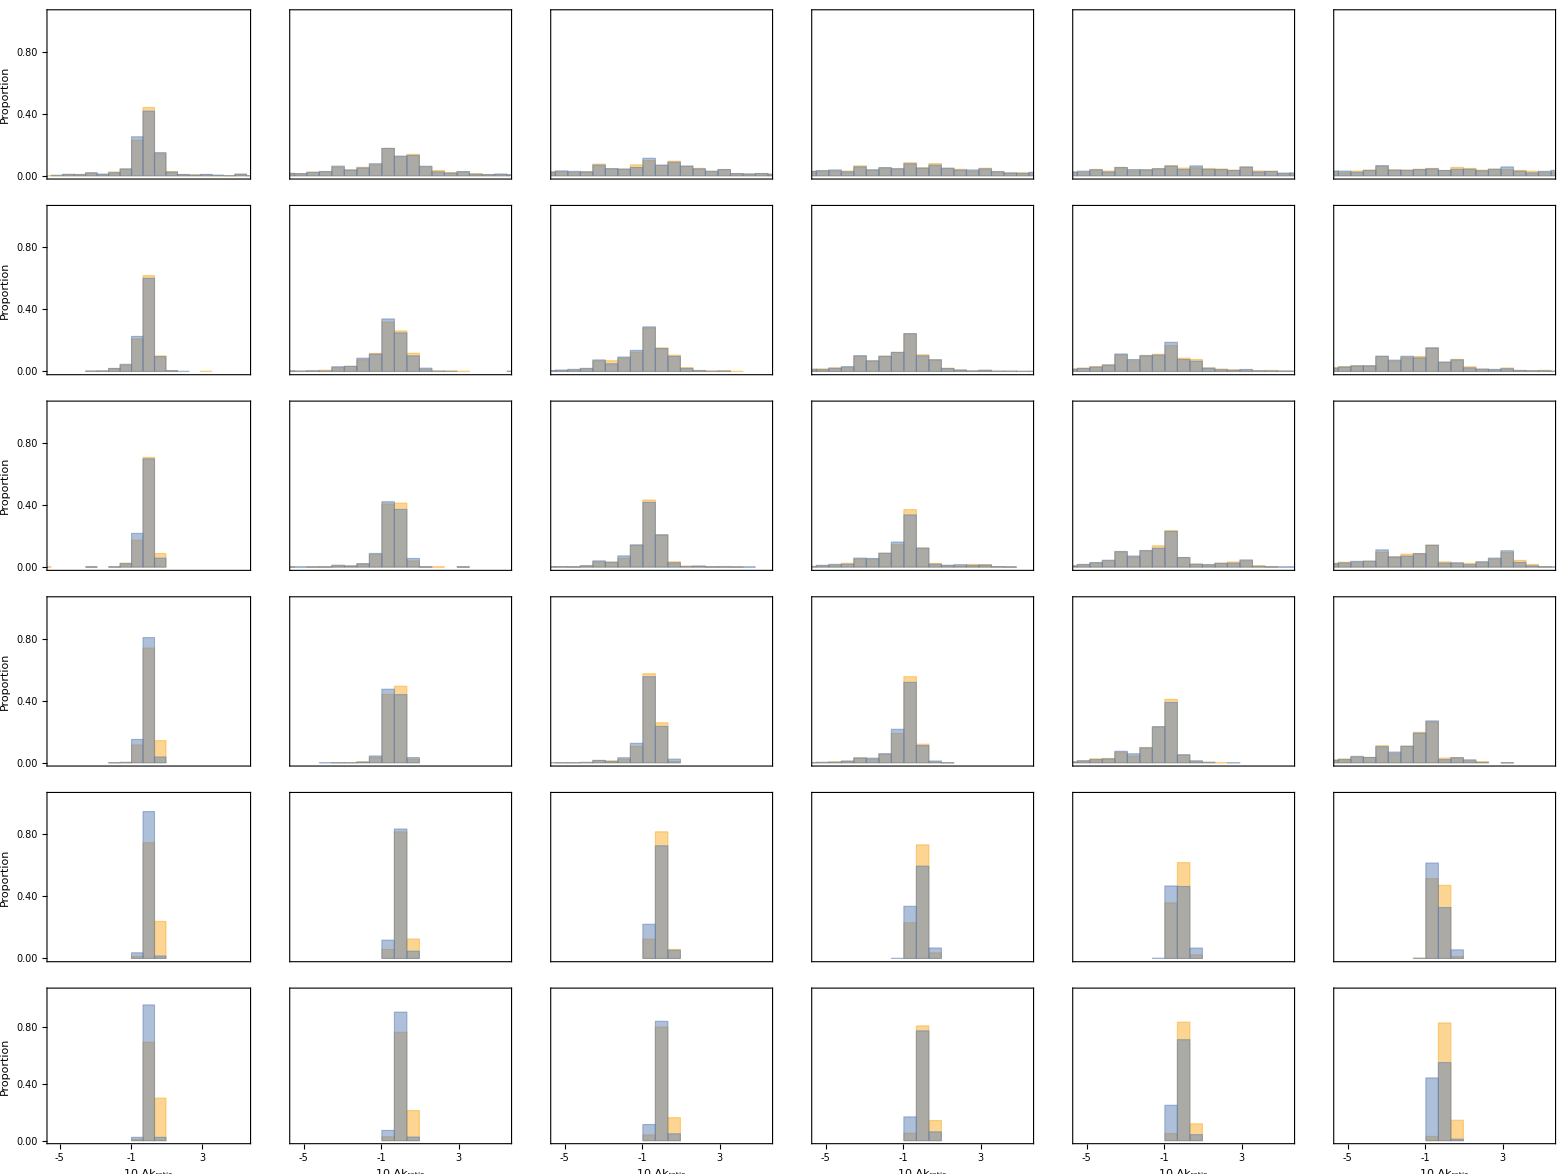

plots/histograms.pdf

```mathematica
p=Grid[Table[ticks={{If[remove==10,Table[{i,PaddedForm[i,{2,2}]},{i,0,1,0.2}],Table[{i,""},{i,0,1,0.2}]],Table[{i,""},{i,0,1,0.2}]},{If[keep==160,Table[{i,Round[10*i]},{i,-0.5,0.5,0.2}],Table[{i,""},{i,-0.5,0.5,0.2}]],Table[{i,""},{i,-0.5,0.5,0.2}]}};
labels={{If[remove==10,"Proportion",None],If[remove==160,Subscript[N,"ret"]==keep,None]},{If[keep==160,Subscript[Δk,"ratio"]*10,None],If[keep==10,Subscript[N,"rem"]==remove,None]}};
imageSize={If[remove==10||remove==160,250,250-70],If[keep==160||keep==10,220,220-40]};
imagePadding={{If[remove==10,75,5],If[remove==160,55,5]},{If[keep==160,55,10],If[keep==10,35,1]}};Histogram[{Log[Cases[rlst1,u_/;u[[3]]==remove&&u[[4]]==keep][[All,6]]]/Log[10],Log[Cases[rlst2,u_/;u[[3]]==remove&&u[[4]]==keep][[All,6]]]/Log[10]},{-1,1,2/31.},"Probability",Axes->False,Frame->True,FrameTicks->ticks,FrameLabel->labels,LabelStyle->Directive[16,Black],FrameStyle->Directive[AbsoluteThickness[1.5],Black],PlotRange->{{-0.55,0.55},{0,1.05}},AspectRatio->1,ImageSize->imageSize,ImagePadding->imagePadding,PlotRangeClipping->True],{keep,10,160,30},{remove,10,160,30}],Spacings->0]
Export["plots/histograms.pdf",p]
```

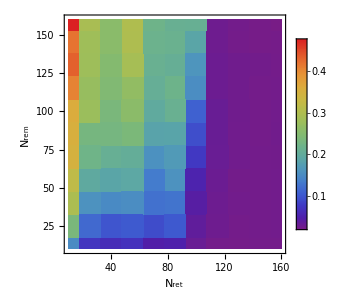
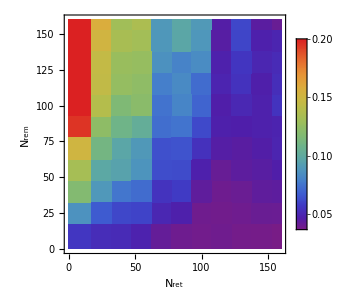
-Graphics- | -Graphics-

stats.pdf

```mathematica
p=Grid[{{ListDensityPlot[Flatten[Table[{keep,remove,StandardDeviation[Cases[diff,u_/;u[[1]]==52&&u[[3]]==remove&&u[[4]]==keep&&u[[6]]≠"failed"][[All,7]]]},{keep,10,160,15},{remove,10,160,15}],1],InterpolationOrder->0,FrameLabel->{{Subscript[N,"rem"],None},{Subscript[N,"ret"],Mean[Subscript[Δk,"ratio"]]}},ClippingStyle->Automatic,LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,PlotLegends->True,ImageSize->300,ColorFunction->"Rainbow"],ListDensityPlot[Flatten[Table[{keep,remove,StandardDeviation[Cases[diff,u_/;u[[1]]==52&&u[[3]]==remove&&u[[4]]==keep&&u[[6]]≠"failed"][[All,6]]]},{keep,10,160,15},{remove,10,160,15}],1],InterpolationOrder->0,FrameLabel->{{Subscript[N,"rem"],None},{Subscript[N,"ret"],StandardDeviation[Subscript[Δk,"ratio"]]}},ClippingStyle->Automatic,LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{0.0,0.2},PlotLegends->True,ImageSize->300,ColorFunction->"Rainbow"]}}]
Export["stats.pdf",p]
```

```mathematica
means37={};
errors37={};
means52={};
errors52={};
senses37={};
senses52={};
Monitor[Do[Do[
cases=Cases[rlst2,u_/;u[[1]]==37&&u[[3]]==remove&&u[[4]]==keep&&Last[u]≠"failed"];If[Length[cases]>0,AppendTo[means37,{keep,remove,Mean[Abs[Log[DeleteCases[cases[[All,6]],u_/;u=="failed"]]/Log[10]]]}];
AppendTo[errors37,{keep,remove,Mean[Log[DeleteCases[cases[[All,7]],u_/;u=="failed"]]/Log[10]]}];AppendTo[senses37,{keep,remove,Mean[DeleteCases[cases[[All,5]],u_/;u=="failed"]/sensitivities[[38]]]}];,AppendTo[means37,{}];
AppendTo[errors37,{}];AppendTo[senses37,{}];];cases=Cases[rlst1,u_/;u[[1]]==52&&u[[3]]==remove&&u[[4]]==keep&&Last[u]≠"failed"];If[Length[cases]>0,AppendTo[means52,{keep,remove,Mean[Abs[Log[DeleteCases[cases[[All,6]],u_/;u=="failed"]]/Log[10]]]}];
AppendTo[errors52,{keep,remove,Mean[Log[DeleteCases[cases[[All,7]],u_/;u=="failed"]]/Log[10]]}];AppendTo[senses52,{keep,remove,Mean[DeleteCases[cases[[All,5]],u_/;u=="failed"]/sensitivities[[53]]]}];,AppendTo[means52,{}];
AppendTo[errors52,{}];AppendTo[senses52,{}];];,{keep,10,160,15}];,{remove,10,160,15}],{keep,remove}]
```

```mathematica
p1=ListDensityPlot[means37,PlotRange->{0,1.0},ClippingStyle->Automatic,InterpolationOrder->0,ColorFunction->"LightTemperatureMap",ImageSize->300,LabelStyle->Directive[16,Black],FrameLabel->{{Subscript[N,"ret"],None},{Subscript[N,"rem"],"Eq. (I)"}},FrameStyle->Directive[AbsoluteThickness[2]],FrameTicks->{{Table[{i,i},{i,10,160,30}],Table[{i,""},{i,10,160,30}]},{Table[{i,""},{i,10,160,30}],Table[{i,""},{i,10,160,30}]}},ImagePadding->{{55,10},{5,55}},AspectRatio->1/2];
p2=ListDensityPlot[means52,PlotRange->{0,1.0},ClippingStyle->Automatic,InterpolationOrder->0,ColorFunction->"LightTemperatureMap",ImageSize->250,LabelStyle->Directive[16,Black],FrameLabel->{{None,None},{None,"Eq. (II)"}},FrameStyle->Directive[AbsoluteThickness[2]],FrameTicks->{{Table[{i,""},{i,10,160,30}],Table[{i,""},{i,10,160,30}]},{Table[{i,""},{i,10,160,30}],Table[{i,""},{i,10,160,30}]}},ImagePadding->{{5,10},{5,55}},AspectRatio->1/2];
p3=ListDensityPlot[senses37,PlotRange->{0,10.0},ClippingStyle->Automatic,PlotRange->All,InterpolationOrder->0,ColorFunction->"LightTemperatureMap",PlotRange->All,InterpolationOrder->0,ColorFunction->"LightTemperatureMap",ImageSize->300,LabelStyle->Directive[16,Black],FrameLabel->{Subscript[N,"ret"],Subscript[N,"rem"]},FrameStyle->Directive[AbsoluteThickness[2]],FrameTicks->{{Table[{i,i},{i,10,160,30}],Table[{i,""},{i,10,160,30}]},{Table[{i,""},{i,10,160,30}],Table[{i,""},{i,10,160,30}]}},ImagePadding->{{55,10},{5,5}},AspectRatio->1/2];
p4=ListDensityPlot[senses52,PlotRange->{0,10.0},ClippingStyle->Automatic,InterpolationOrder->0,ColorFunction->"LightTemperatureMap",ImageSize->250,LabelStyle->Directive[16,Black],FrameLabel->{Subscript[N,"ret"],None},FrameStyle->Directive[AbsoluteThickness[2]],FrameTicks->{{Table[{i,""},{i,10,160,30}],Table[{i,""},{i,10,160,30}]},{Table[{i,""},{i,10,160,30}],Table[{i,""},{i,10,160,30}]}},ImagePadding->{{5,10},{5,5}},AspectRatio->1/2];
p5=ListDensityPlot[errors37,PlotRange->{-2,0},ClippingStyle->Automatic,InterpolationOrder->0,ColorFunction->"LightTemperatureMap",PlotRange->All,InterpolationOrder->0,ColorFunction->"LightTemperatureMap",ImageSize->300,LabelStyle->Directive[16,Black],FrameLabel->{Subscript[N,"ret"],Subscript[N,"rem"]},FrameStyle->Directive[AbsoluteThickness[2]],FrameTicks->{{Table[{i,i},{i,10,160,30}],Table[{i,""},{i,10,160,30}]},{Table[{i,i},{i,10,160,30}],Table[{i,""},{i,10,160,30}]}},ImagePadding->{{55,10},{55,5}},AspectRatio->1/2];
p6=ListDensityPlot[errors52,PlotRange->{-2,0},ClippingStyle->Automatic,InterpolationOrder->0,ColorFunction->"LightTemperatureMap",ImageSize->250,LabelStyle->Directive[16,Black],FrameLabel->{Subscript[N,"ret"],None},FrameStyle->Directive[AbsoluteThickness[2]],FrameTicks->{{Table[{i,""},{i,10,160,30}],Table[{i,""},{i,10,160,30}]},{Table[{i,i},{i,10,160,30}],Table[{i,""},{i,10,160,30}]}},ImagePadding->{{5,10},{55,5}},AspectRatio->1/2];
p=Grid[{{rasterizeBackground[p1],Grid[{{rasterizeBackground[p2],BarLegend[{"LightTemperatureMap",{0,1.0}},LabelStyle->Directive[Black,14],LegendLabel->Abs[DisplayForm[Subscript[log,10][RowBox[{Subscript[k,est],"/",Subscript[k,0]}]]]],ImageSize->{250,125}]}}]},{rasterizeBackground[p3],Grid[{{rasterizeBackground[p4],BarLegend[{"LightTemperatureMap",{0,10.0}},LabelStyle->Directive[Black,14],LegendLabel->DisplayForm[RowBox[{Subscript[S,"remove"],"/",Subscript[S,"measure"]}]],ImageSize->{250,125}]}}]},{rasterizeBackground[p5],Grid[{{rasterizeBackground[p6],BarLegend[{"LightTemperatureMap",{-2,0}},LabelStyle->Directive[Black,14],LegendLabel->Subscript[log,10][ϵ],ImageSize->{250,125}]}}]}},Alignment->Left]
Export["plots/averages.pdf",p]
```

-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- |

plots/averages.pdf

```mathematica
d1=DeleteCases[Table[If[rlst1[[i,6]]≠"failed"&&rlst2[[i,6]]≠"failed"&&Abs[Log[rlst1[[i,6]]]/Log[10]]<1&&Abs[Log[rlst2[[i,6]]]/Log[10]]<1,rlst1[[i,6]]],{i,1,Length[rlst1]}],Null];d2=DeleteCases[Table[If[rlst1[[i,6]]≠"failed"&&rlst2[[i,6]]≠"failed"&&Abs[Log[rlst1[[i,6]]]/Log[10]]<1&&Abs[Log[rlst2[[i,6]]]/Log[10]]<1,rlst2[[i,6]]],{i,1,Length[rlst1]}],Null];
p=ListLogLogPlot[Transpose[{d1,d2}],PlotRange->All,Axes->False,Frame->True,FrameLabel->{DisplayForm[RowBox[{Subsuperscript[k,est,Ar+air],"/",Subscript[k,0]}]],DisplayForm[RowBox[{Subsuperscript[k,est,air],"/",Subscript[k,0]}]]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]]]
Export["plots/dilute.pdf",rasterizeBackground[p]]
Correlation[d1,d2]
```

-Graphics-

plots/dilute.pdf

0.886986

```mathematica
Length[d1]
Length[d2]
```

2000

2000

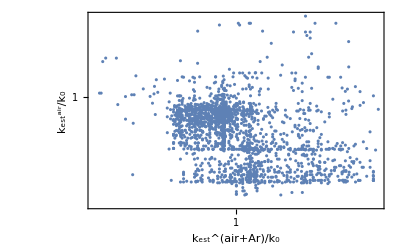

```mathematica
d1=DeleteCases[Table[If[rlst1[[i,6]]≠"failed"&&rlst2[[i,6]]≠"failed"&&Abs[Log[rlst1[[i,6]]]/Log[10]]<1&&Abs[Log[rlst2[[i,6]]]/Log[10]]<1&&rlst1[[i,3]]==160&&rlst1[[i,4]]==160,rlst1[[i,6]]],{i,1,Length[rlst1]}],Null];d2=DeleteCases[Table[If[rlst1[[i,6]]≠"failed"&&rlst2[[i,6]]≠"failed"&&Abs[Log[rlst1[[i,6]]]/Log[10]]<1&&Abs[Log[rlst2[[i,6]]]/Log[10]]<1&&rlst1[[i,3]]==160&&rlst1[[i,4]]==160,rlst2[[i,6]]],{i,1,Length[rlst1]}],Null];
ListLogLogPlot[Transpose[{d1,d2}],PlotRange->All,Axes->False,Frame->True,FrameLabel->{DisplayForm[RowBox[{Subsuperscript[k,est,Ar+air],"/",Subscript[k,0]}]],DisplayForm[RowBox[{Subsuperscript[k,est,air],"/",Subscript[k,0]}]]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]]]
```

Acceptable parameters

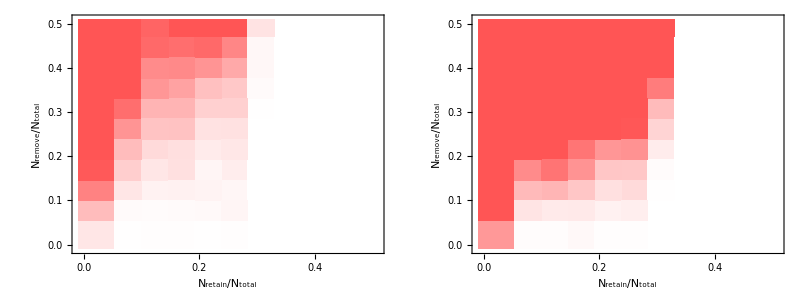

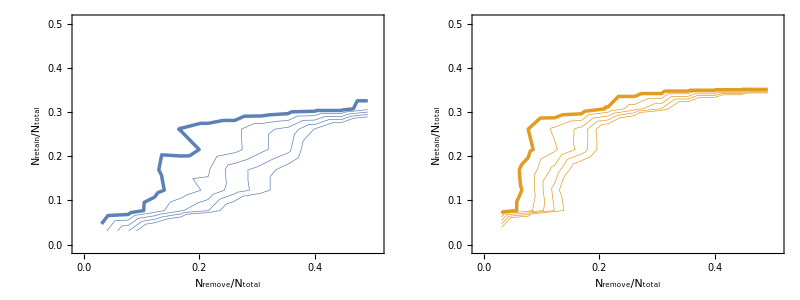

reaction1.dat

reaction2.dat

```mathematica
test1={#[[1]],#[[2]],Count[#[[3]],u_/;u>Log[2.0]/Log[10]]/Length[#[[3]]]}&/@DeleteCases[Flatten[Table[{keep/nreactions,remove/nreactions,Abs[Log[Cases[rlst1,u_/;First[u]==37&&u[[3]]==remove&&u[[4]]==keep&&u[[6]]≠"failed"][[All,6]]]/Log[10]]},{keep,10,160,15},{remove,10,160,15}],1],u_/;Last[u]=={}];
test2={#[[1]],#[[2]],Count[#[[3]],u_/;u>Log[2.0]/Log[10]]/Length[#[[3]]]}&/@DeleteCases[Flatten[Table[{keep/nreactions,remove/nreactions,Abs[Log[Cases[rlst1,u_/;First[u]==52&&u[[3]]==remove&&u[[4]]==keep&&u[[6]]≠"failed"][[All,6]]]/Log[10]]},{keep,10,160,15},{remove,10,160,15}],1],u_/;Last[u]=={}];
Grid[{{ListDensityPlot[test1,InterpolationOrder->0,PlotRange->{{-0.01,0.51},{-0.01,0.51},All},ColorFunction->(Blend[{White,Lighter[Red]},#/(0.2)]&),ColorFunctionScaling->False,FrameLabel->{DisplayForm[RowBox[{Subscript[N,"retain"],"/",Subscript[N,"total"]}]],DisplayForm[RowBox[{Subscript[N,"remove"],"/",Subscript[N,"total"]}]]},LabelStyle->Directive[16,Black],FrameStyle->Black,ImageSize->250,ImagePadding->{{55,5},{55,5}},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]}}],ListDensityPlot[test2,InterpolationOrder->0,PlotRange->{{-0.01,0.51},{-0.01,0.51},All},ColorFunction->(Blend[{White,Lighter[Red]},#/(0.2)]&),ColorFunctionScaling->False,FrameLabel->{DisplayForm[RowBox[{Subscript[N,"retain"],"/",Subscript[N,"total"]}]],DisplayForm[RowBox[{Subscript[N,"remove"],"/",Subscript[N,"total"]}]]},LabelStyle->Directive[16,Black],FrameStyle->Black,ImageSize->250,ImagePadding->{{55,5},{55,5}},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]}}]}}]
Grid[{{ListContourPlot[{#[[2]],#[[1]],#[[3]]}&/@test1,InterpolationOrder->1,PlotRange->{{-0.01,0.51},{-0.01,0.51},All},ColorFunctionScaling->False,FrameLabel->{{DisplayForm[RowBox[{Subscript[N,"retain"],"/",Subscript[N,"total"]}]],None},{DisplayForm[RowBox[{Subscript[N,"remove"],"/",Subscript[N,"total"]}]],None}},LabelStyle->Directive[16,Black],FrameStyle->{Black,AbsoluteThickness[1.5]}, ImageSize->250,ImagePadding->{{55,5},{55,55}},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]}},Contours->Table[i,{i,0.02,0.1,0.02}],ContourShading->None,ContourStyle->Join[{Directive[Thickness[0.01],ColorData[97,"ColorList"][[1]],Opacity[1]]},ConstantArray[Directive[Thickness[0.002],ColorData[97,"ColorList"][[1]],Opacity[1]],4]]],ListContourPlot[{#[[2]],#[[1]],#[[3]]}&/@test2,InterpolationOrder->1,PlotRange->{{-0.01,0.51},{-0.01,0.51},All},ColorFunctionScaling->False,FrameLabel->{{DisplayForm[RowBox[{Subscript[N,"retain"],"/",Subscript[N,"total"]}]],None},{DisplayForm[RowBox[{Subscript[N,"remove"],"/",Subscript[N,"total"]}]],None}},LabelStyle->Directive[16,Black],FrameStyle->{Black,AbsoluteThickness[1.5]}, ImageSize->250,ImagePadding->{{55,5},{55,55}},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]}},Contours->Table[i,{i,0.02,0.1,0.02}],ContourShading->None,ContourStyle->Join[{Directive[Thickness[0.01],ColorData[97,"ColorList"][[2]],Opacity[1]]},ConstantArray[Directive[Thickness[0.002],ColorData[97,"ColorList"][[2]],Opacity[1]],4]]]}}]
Export["reaction1.dat", test1]
Export["reaction2.dat",test2]
```

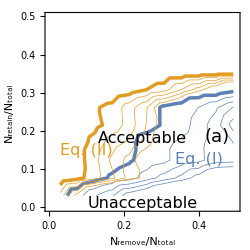

```mathematica
test1=ToExpression[Import["reaction1.dat"]];
test2=ToExpression[Import["reaction2.dat"]];
p1=ListContourPlot[{#[[2]],#[[1]],#[[3]]}&/@test1,InterpolationOrder->10,PlotRange->{{-0.01,0.51},{-0.01,0.21},All},ColorFunctionScaling->False,FrameLabel->{{DisplayForm[RowBox[{Subscript[N,"retain"],"/",Subscript[N,"total"]}]],None},{DisplayForm[RowBox[{Subscript[N,"remove"],"/",Subscript[N,"total"]}]],"Combustion"}},LabelStyle->Directive[16,Black],FrameStyle->{Black,AbsoluteThickness[1.5]},ImageSize->250,ImagePadding->{{55,10},{55,55}},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]}},Contours->Table[i,{i,0.05,0.25,0.05}],ContourShading->None,ContourStyle->Join[{Directive[Thickness[0.01],ColorData[97,"ColorList"][[1]],Opacity[1]]},ConstantArray[Directive[Thickness[0.002],ColorData[97,"ColorList"][[1]],Opacity[1]],4]]];
p2=ListContourPlot[{#[[2]],#[[1]],#[[3]]}&/@test2,InterpolationOrder->10,PlotRange->{{-0.01,0.51},{-0.01,0.21},All},ColorFunctionScaling->False,FrameLabel->{{DisplayForm[RowBox[{Subscript[N,"retain"],"/",Subscript[N,"total"]}]],None},{DisplayForm[RowBox[{Subscript[N,"remove"],"/",Subscript[N,"total"]}]],None}},LabelStyle->Directive[16,Black],FrameStyle->{Black,AbsoluteThickness[1.5]}, ImageSize->250,ImagePadding->{{55,10},{55,55}},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]}},Contours->Table[i,{i,0.05,0.25,0.05}],ContourShading->None,ContourStyle->Join[{Directive[Thickness[0.01],ColorData[97,"ColorList"][[2]],Opacity[1]]},ConstantArray[Directive[Thickness[0.002],ColorData[97,"ColorList"][[2]],Opacity[1]],4]]];
Show[p1,p2,Epilog->{Inset[Style["Acceptable",16],{0.25,0.18}],Inset[Style["Unacceptable",16],{0.25,0.01}],Inset[Style["Eq. (I)",Directive[16,ColorData[97,"ColorList"][[1]]]],{0.4,0.125},Background->White],Inset[Style["Eq. (II)", Directive[16,ColorData[97,"ColorList"][[2]]]],{0.1,0.15},Background->White],Inset[Style["(a)",18],{0.45,0.185}]},PlotRange->{{0,0.5},{0,0.5}}]
```

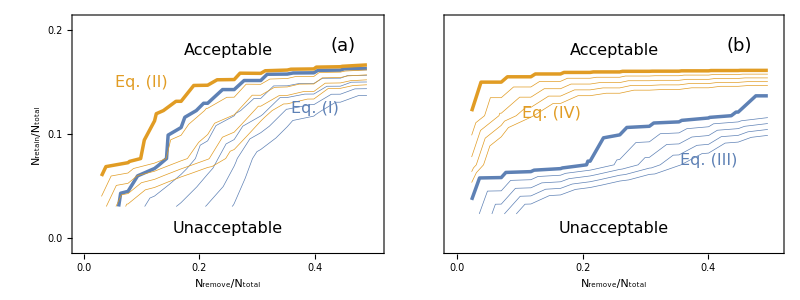

fig6.pdf

```mathematica
test1=ToExpression[Import["reaction1.dat"]];
test2=ToExpression[Import["reaction2.dat"]];
test3=ToExpression[Import["../cvd/reaction3.dat"]];
test4=ToExpression[Import["../cvd/reaction4.dat"]];
p1=ListContourPlot[{#[[2]],#[[1]],#[[3]]}&/@test1,InterpolationOrder->10,PlotRange->{{-0.01,0.51},{-0.01,0.21},All},ColorFunctionScaling->False,FrameLabel->{{DisplayForm[RowBox[{Subscript[N,"retain"],"/",Subscript[N,"total"]}]],None},{DisplayForm[RowBox[{Subscript[N,"remove"],"/",Subscript[N,"total"]}]],"Combustion"}},LabelStyle->Directive[16,Black],FrameStyle->{Black,AbsoluteThickness[1.5]},ImageSize->250,ImagePadding->{{55,10},{55,55}},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]}},Contours->Table[i,{i,0.05,0.25,0.05}],ContourShading->None,ContourStyle->Join[{Directive[Thickness[0.01],ColorData[97,"ColorList"][[1]],Opacity[1]]},ConstantArray[Directive[Thickness[0.002],ColorData[97,"ColorList"][[1]],Opacity[1]],4]]];
p2=ListContourPlot[{#[[2]],#[[1]],#[[3]]}&/@test2,InterpolationOrder->10,PlotRange->{{-0.01,0.51},{-0.01,0.21},All},ColorFunctionScaling->False,FrameLabel->{{DisplayForm[RowBox[{Subscript[N,"retain"],"/",Subscript[N,"total"]}]],None},{DisplayForm[RowBox[{Subscript[N,"remove"],"/",Subscript[N,"total"]}]],None}},LabelStyle->Directive[16,Black],FrameStyle->{Black,AbsoluteThickness[1.5]}, ImageSize->250,ImagePadding->{{55,10},{55,55}},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]}},Contours->Table[i,{i,0.05,0.25,0.05}],ContourShading->None,ContourStyle->Join[{Directive[Thickness[0.01],ColorData[97,"ColorList"][[2]],Opacity[1]]},ConstantArray[Directive[Thickness[0.002],ColorData[97,"ColorList"][[2]],Opacity[1]],4]]];
p3=ListContourPlot[{#[[2]],#[[1]],#[[3]]}&/@test3,InterpolationOrder->10,PlotRange->{{-0.01,0.51},{-0.01,0.21},All},ColorFunctionScaling->False,FrameLabel->{{None,None},{DisplayForm[RowBox[{Subscript[N,"remove"],"/",Subscript[N,"total"]}]],"Pyrolysis"}},LabelStyle->Directive[16,Black],FrameStyle->{Black,AbsoluteThickness[1.5]},ImageSize->250,ImagePadding->{{10,55},{55,55}},FrameTicks->{{Table[{i,""},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]}},Contours->Table[i,{i,0.05,0.25,0.05}],ContourShading->None,ContourStyle->Join[{Directive[Thickness[0.01],ColorData[97,"ColorList"][[1]],Opacity[1]]},ConstantArray[Directive[Thickness[0.002],ColorData[97,"ColorList"][[1]],Opacity[1]],4]]];
p4=ListContourPlot[{#[[2]],#[[1]],#[[3]]}&/@test4,InterpolationOrder->10,PlotRange->{{-0.01,0.51},{-0.01,0.21},All},ColorFunctionScaling->False,FrameLabel->{{None,None},{DisplayForm[RowBox[{Subscript[N,"remove"],"/",Subscript[N,"total"]}]],None}},LabelStyle->Directive[16,Black],FrameStyle->{Black,AbsoluteThickness[1.5]},ImageSize->250,ImagePadding->{{10,55},{55,5}},FrameTicks->{{Table[{i,""},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]}},Contours->Table[i,{i,0.05,0.25,0.05}],ContourShading->None,ContourStyle->Join[{Directive[Thickness[0.01],ColorData[97,"ColorList"][[2]],Opacity[1]]},ConstantArray[Directive[Thickness[0.002],ColorData[97,"ColorList"][[2]],Opacity[1]],4]]];
p=Grid[{{Show[p1,p2,Epilog->{Inset[Style["Acceptable",16],{0.25,0.18}],Inset[Style["Unacceptable",16],{0.25,0.01}],Inset[Style["Eq. (I)",Directive[16,ColorData[97,"ColorList"][[1]]]],{0.4,0.125},Background->White],Inset[Style["Eq. (II)", Directive[16,ColorData[97,"ColorList"][[2]]]],{0.1,0.15},Background->White],Inset[Style["(a)",18],{0.45,0.185}]}],Show[p3,p4,Epilog->{Inset[Style["Acceptable",16],{0.25,0.18}],Inset[Style["Unacceptable",16],{0.25,0.01}],Inset[Style["Eq. (III)",Directive[16,ColorData[97,"ColorList"][[1]]],Background->White],{0.4,0.075}],Inset[Style["Eq. (IV)",Directive[16,ColorData[97,"ColorList"][[2]]],Background->White],{0.15,0.12}],Inset[Style["(b)",18],{0.45,0.185}]}]}}]
Export["fig6.pdf",p]
```